```mathematica
(*Hamiltonian of unitcell*)
unitcell[ω_,δ_,t_,ϵ_,m_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
(*Hopping between two unitcells*)
VLR[t_,m_]:=t*IdentityMatrix[m]
```

```mathematica
Recursivefunction[ω_,δ_,t_,ϵ_,m_,X_]:=Module[{J=Inverse[unitcell[ω,δ,t,ϵ,m]],A:=Inverse[unitcell[ω,δ,t,ϵ,m]],T:=VLR[t,m]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,X];J=J]
```

```mathematica
Clear[LEFT]
```

```mathematica
Monitor[Table[Export["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[x]<>"_lead_"<>ToString[ω]<>"_.dat",LEFT[ω,0.0001,1,0,50]],{ω,Range[0.71,3,0.01]}],ω]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{2.94117×10^6+0.00028337 ⅈ,-2.94117×10^6+0.0013181 ⅈ,1.55381×10^-7-0.00310588 ⅈ,2.94117×10^6+0.00178778 ⅈ,-2.94117×10^6+0.00263427 ⅈ,2.82442×10^-7-0.00564705 ⅈ,«38»,1.67467×10^-7-0.00335293 ⅈ,2.94118×10^6+0.00154072 ⅈ,-2.94118×10^6+0.000987217 ⅈ,8.45952×10^-8-0.00169411 ⅈ,2.94118×10^6+0.000706897 ⅈ,-2.94118×10^6+0.000141631 ⅈ},{«1»},«46»,{«1»},{«1»}} may contain significant numerical errors.

{/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.71_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.72_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.73_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.74_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.75_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.76_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.77_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.78_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.79_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.8_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.81_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.82_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.83_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.84_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.85_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.86_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.87_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.88_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.89_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.9_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.91_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.92_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.93_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.94_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.95_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.96_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.97_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.98_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_0.99_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1._.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.01_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.02_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.03_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.04_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.05_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.06_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.07_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.08_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.09_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.1_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.11_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.12_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.13_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.14_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.15_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.16_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.17_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.18_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.19_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.2_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.21_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.22_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.23_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.24_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.25_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.26_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.27_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.28_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.29_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.3_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.31_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.32_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.33_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.34_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.35_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.36_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.37_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.38_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.39_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.4_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.41_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.42_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.43_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.44_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.45_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.46_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.47_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.48_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.49_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.5_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.51_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.52_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.53_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.54_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.55_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.56_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.57_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.58_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.59_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.6_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.61_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.62_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.63_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.64_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.65_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.66_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.67_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.68_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.69_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.7_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.71_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.72_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.73_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.74_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.75_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.76_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.77_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.78_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.79_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.8_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.81_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.82_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.83_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.84_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.85_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.86_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.87_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.88_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.89_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.9_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.91_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.92_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.93_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.94_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.95_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.96_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.97_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.98_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_1.99_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2._.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.01_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.02_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.03_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.04_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.05_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.06_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.07_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.08_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.09_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.1_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.11_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.12_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.13_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.14_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.15_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.16_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.17_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.18_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.19_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.2_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.21_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.22_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.23_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.24_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.25_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.26_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.27_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.28_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.29_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.3_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.31_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.32_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.33_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.34_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.35_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.36_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.37_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.38_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.39_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.4_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.41_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.42_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.43_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.44_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.45_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.46_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.47_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.48_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.49_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.5_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.51_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.52_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.53_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.54_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.55_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.56_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.57_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.58_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.59_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.6_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.61_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.62_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.63_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.64_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.65_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.66_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.67_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.68_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.69_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.7_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.71_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.72_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.73_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.74_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.75_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.76_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.77_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.78_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.79_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.8_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.81_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.82_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.83_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.84_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.85_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.86_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.87_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.88_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.89_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.9_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.91_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.92_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.93_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.94_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.95_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.96_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.97_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.98_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_2.99_.dat,/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_x_lead_3._.dat}

```mathematica
Clear[LEFT]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].
g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris=Compile[{ω},tr[ω,0.0001,5,0,100],CompilationTarget->"C",Parallelization->True]
```

CompiledFunction[…]

```mathematica
Table[{ω,-Im[IL[ω,0.0001,1,0,10][[5,5]]];Print["Energy "<>ToString[ω]<>" done"]},{ω,Range[0,4,0.01]}]
```

{{0.,Null},{0.01,Null},{0.02,Null},{0.03,Null},{0.04,Null},{0.05,Null},{0.06,Null},{0.07,Null},{0.08,Null},{0.09,Null},{0.1,Null},{0.11,Null},{0.12,Null},{0.13,Null},{0.14,Null},{0.15,Null},{0.16,Null},{0.17,Null},{0.18,Null},{0.19,Null},{0.2,Null},{0.21,Null},{0.22,Null},{0.23,Null},{0.24,Null},{0.25,Null},{0.26,Null},{0.27,Null},{0.28,Null},{0.29,Null},{0.3,Null},{0.31,Null},{0.32,Null},{0.33,Null},{0.34,Null},{0.35,Null},{0.36,Null},{0.37,Null},{0.38,Null},{0.39,Null},{0.4,Null},{0.41,Null},{0.42,Null},{0.43,Null},{0.44,Null},{0.45,Null},{0.46,Null},{0.47,Null},{0.48,Null},{0.49,Null},{0.5,Null},{0.51,Null},{0.52,Null},{0.53,Null},{0.54,Null},{0.55,Null},{0.56,Null},{0.57,Null},{0.58,Null},{0.59,Null},{0.6,Null},{0.61,Null},{0.62,Null},{0.63,Null},{0.64,Null},{0.65,Null},{0.66,Null},{0.67,Null},{0.68,Null},{0.69,Null},{0.7,Null},{0.71,Null},{0.72,Null},{0.73,Null},{0.74,Null},{0.75,Null},{0.76,Null},{0.77,Null},{0.78,Null},{0.79,Null},{0.8,Null},{0.81,Null},{0.82,Null},{0.83,Null},{0.84,Null},{0.85,Null},{0.86,Null},{0.87,Null},{0.88,Null},{0.89,Null},{0.9,Null},{0.91,Null},{0.92,Null},{0.93,Null},{0.94,Null},{0.95,Null},{0.96,Null},{0.97,Null},{0.98,Null},{0.99,Null},{1.,Null},{1.01,Null},{1.02,Null},{1.03,Null},{1.04,Null},{1.05,Null},{1.06,Null},{1.07,Null},{1.08,Null},{1.09,Null},{1.1,Null},{1.11,Null},{1.12,Null},{1.13,Null},{1.14,Null},{1.15,Null},{1.16,Null},{1.17,Null},{1.18,Null},{1.19,Null},{1.2,Null},{1.21,Null},{1.22,Null},{1.23,Null},{1.24,Null},{1.25,Null},{1.26,Null},{1.27,Null},{1.28,Null},{1.29,Null},{1.3,Null},{1.31,Null},{1.32,Null},{1.33,Null},{1.34,Null},{1.35,Null},{1.36,Null},{1.37,Null},{1.38,Null},{1.39,Null},{1.4,Null},{1.41,Null},{1.42,Null},{1.43,Null},{1.44,Null},{1.45,Null},{1.46,Null},{1.47,Null},{1.48,Null},{1.49,Null},{1.5,Null},{1.51,Null},{1.52,Null},{1.53,Null},{1.54,Null},{1.55,Null},{1.56,Null},{1.57,Null},{1.58,Null},{1.59,Null},{1.6,Null},{1.61,Null},{1.62,Null},{1.63,Null},{1.64,Null},{1.65,Null},{1.66,Null},{1.67,Null},{1.68,Null},{1.69,Null},{1.7,Null},{1.71,Null},{1.72,Null},{1.73,Null},{1.74,Null},{1.75,Null},{1.76,Null},{1.77,Null},{1.78,Null},{1.79,Null},{1.8,Null},{1.81,Null},{1.82,Null},{1.83,Null},{1.84,Null},{1.85,Null},{1.86,Null},{1.87,Null},{1.88,Null},{1.89,Null},{1.9,Null},{1.91,Null},{1.92,Null},{1.93,Null},{1.94,Null},{1.95,Null},{1.96,Null},{1.97,Null},{1.98,Null},{1.99,Null},{2.,Null},{2.01,Null},{2.02,Null},{2.03,Null},{2.04,Null},{2.05,Null},{2.06,Null},{2.07,Null},{2.08,Null},{2.09,Null},{2.1,Null},{2.11,Null},{2.12,Null},{2.13,Null},{2.14,Null},{2.15,Null},{2.16,Null},{2.17,Null},{2.18,Null},{2.19,Null},{2.2,Null},{2.21,Null},{2.22,Null},{2.23,Null},{2.24,Null},{2.25,Null},{2.26,Null},{2.27,Null},{2.28,Null},{2.29,Null},{2.3,Null},{2.31,Null},{2.32,Null},{2.33,Null},{2.34,Null},{2.35,Null},{2.36,Null},{2.37,Null},{2.38,Null},{2.39,Null},{2.4,Null},{2.41,Null},{2.42,Null},{2.43,Null},{2.44,Null},{2.45,Null},{2.46,Null},{2.47,Null},{2.48,Null},{2.49,Null},{2.5,Null},{2.51,Null},{2.52,Null},{2.53,Null},{2.54,Null},{2.55,Null},{2.56,Null},{2.57,Null},{2.58,Null},{2.59,Null},{2.6,Null},{2.61,Null},{2.62,Null},{2.63,Null},{2.64,Null},{2.65,Null},{2.66,Null},{2.67,Null},{2.68,Null},{2.69,Null},{2.7,Null},{2.71,Null},{2.72,Null},{2.73,Null},{2.74,Null},{2.75,Null},{2.76,Null},{2.77,Null},{2.78,Null},{2.79,Null},{2.8,Null},{2.81,Null},{2.82,Null},{2.83,Null},{2.84,Null},{2.85,Null},{2.86,Null},{2.87,Null},{2.88,Null},{2.89,Null},{2.9,Null},{2.91,Null},{2.92,Null},{2.93,Null},{2.94,Null},{2.95,Null},{2.96,Null},{2.97,Null},{2.98,Null},{2.99,Null},{3.,Null},{3.01,Null},{3.02,Null},{3.03,Null},{3.04,Null},{3.05,Null},{3.06,Null},{3.07,Null},{3.08,Null},{3.09,Null},{3.1,Null},{3.11,Null},{3.12,Null},{3.13,Null},{3.14,Null},{3.15,Null},{3.16,Null},{3.17,Null},{3.18,Null},{3.19,Null},{3.2,Null},{3.21,Null},{3.22,Null},{3.23,Null},{3.24,Null},{3.25,Null},{3.26,Null},{3.27,Null},{3.28,Null},{3.29,Null},{3.3,Null},{3.31,Null},{3.32,Null},{3.33,Null},{3.34,Null},{3.35,Null},{3.36,Null},{3.37,Null},{3.38,Null},{3.39,Null},{3.4,Null},{3.41,Null},{3.42,Null},{3.43,Null},{3.44,Null},{3.45,Null},{3.46,Null},{3.47,Null},{3.48,Null},{3.49,Null},{3.5,Null},{3.51,Null},{3.52,Null},{3.53,Null},{3.54,Null},{3.55,Null},{3.56,Null},{3.57,Null},{3.58,Null},{3.59,Null},{3.6,Null},{3.61,Null},{3.62,Null},{3.63,Null},{3.64,Null},{3.65,Null},{3.66,Null},{3.67,Null},{3.68,Null},{3.69,Null},{3.7,Null},{3.71,Null},{3.72,Null},{3.73,Null},{3.74,Null},{3.75,Null},{3.76,Null},{3.77,Null},{3.78,Null},{3.79,Null},{3.8,Null},{3.81,Null},{3.82,Null},{3.83,Null},{3.84,Null},{3.85,Null},{3.86,Null},{3.87,Null},{3.88,Null},{3.89,Null},{3.9,Null},{3.91,Null},{3.92,Null},{3.93,Null},{3.94,Null},{3.95,Null},{3.96,Null},{3.97,Null},{3.98,Null},{3.99,Null},{4.,Null}}

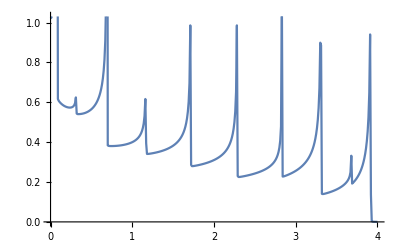

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0,10][[5,5]]]},{ω,Range[0,4,0.01]}]]
```

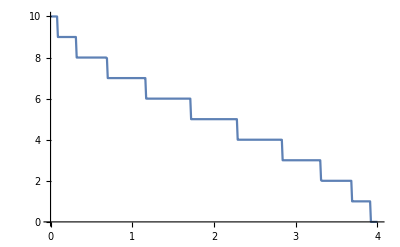

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0,10]},{ω,Range[0,4,0.01]}]]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2.49,0.01]}]
```